## Data

```mathematica
SetDirectory[NotebookDirectory[]];
data=Import ["task2.csv"];
claassMinus1=data[[Flatten@Position[data[[All,3]],-1]]];
claassMinus2=data[[Flatten@Position[data[[All,3]],1]]];
```

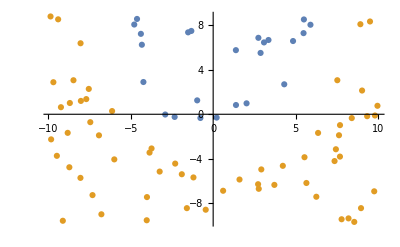

```mathematica
ListPlot[{claassMinus1[[All,;;2]],claassMinus2[[All,;;2]]}]
```

## Poly Kernel